## Constant pressure kappa_ph

## Import phonopy Data;

```mathematica
fileKappa={"t_kappa_31.ISO.0.01bmf.dat","t_kappa_31.ISO.0.1bmf.dat","t_kappa_31.ISO.1bmf.dat","t_kappa_31.ISO.10bmf.dat","t_kappa_31.ISO.100bmf.dat","t_kappa_31.ISO.BULK.dat","t_kappa_31.PERF.BULK.dat"};

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/noZP_0/"];
kappa0=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/10/"];
kappa10=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/300/"];
kappa300=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/760/"];
kappa760=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/1000/"];
kappa1000=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/1500/"];
kappa1500=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/2500/"];
kappa2500=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];

SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/3800/"];
kappa3800=Table[ReadList[fileKappa[[i]],{Number, Number}],{i,1,fileKappa//Length}];
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/PBE10/"];
kappa10PBE=ReadList["t_kappa_31.ISO.BULK.dat",{Number, Number}];
```

## Import compressive sensing data

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/OUT_ZrC_CS/"];
fileCS={"kappa-T-0", "kappa-T-300", "kappa-T-1000","kappa-T-1500","kappa-T-2500" ,"kappa-T-3800","kappa-T-3800-SCPH-3800"};
csCond=Table[ReadList[fileCS[[i]],{Number, Number,Number, Number,Number, Number,Number,Number, Number,Number,Number}],{i,1,fileCS//Length}];
condCS=Table[Transpose@{Transpose[csCond[[i]]][[1]],Transpose[csCond[[i]]][[3]]},{i,1,fileCS//Length}];
condCS//Length
```

7

## Plot BULK phono3py kappa(T) at different volumes;

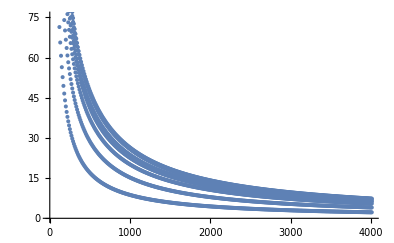

```mathematica
With[{b1=6,b2=6},Show[{ListPlot[kappa10[[b1;;b2]]],ListPlot[kappa300[[b1;;b2]]],ListPlot[kappa760[[b1;;b2]]],ListPlot[kappa1000[[b1;;b2]]],ListPlot[kappa1500[[b1;;b2]]],ListPlot[kappa2500[[b1;;b2]]],ListPlot[kappa3800[[b1;;b2]]]}]]
```

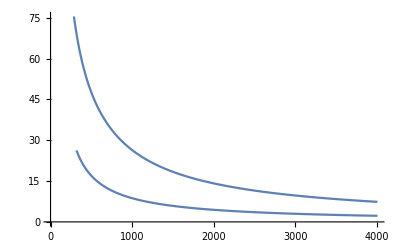

```mathematica
Show[{ListLinePlot@kappa10[[6]],ListLinePlot@kappa3800[[6]]}]
```

#### Compare PBE and LDA

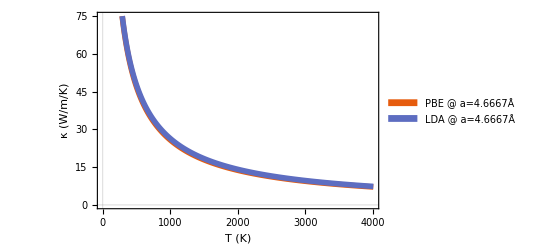

```mathematica
ListLinePlot[{kappa10PBE,kappa10[[6]]},Frame->True,FrameStyle->Directive[Black,20,Thickness[0.004]],FrameLabel->{"T (K)","κ (W/m/K)"},PlotStyle->Thickness[0.01],PlotTheme->"Scientific",PlotLegends->Placed[SwatchLegend[{Style["PBE  @ a=4.6667Å",18,Black],Style["LDA @ a=4.6667Å",18,Black]}],{Right,Top}]]
```

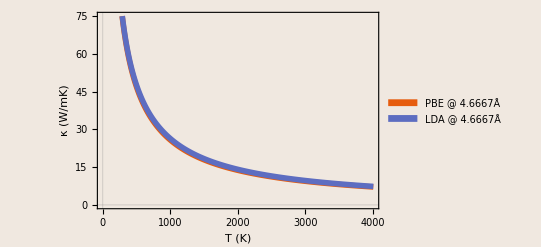

```mathematica
ListLinePlot[{kappa10PBE,kappa10[[6]]},Frame->True,FrameStyle->Directive[Black,20,Thickness[0.004]],FrameLabel->{"T (K)","κ (W/m/K)"},PlotStyle->Thickness[0.01],PlotTheme->"Scientific",PlotLegends->Placed[SwatchLegend[{Style["PBE  @ 4.6667Å",18,Black],Style["LDA @ 4.6667Å",18,Black]}],{Right,Top}],Background->LightBrown]
```

## Plot phono3py and CS kappa(T) at different volumes;

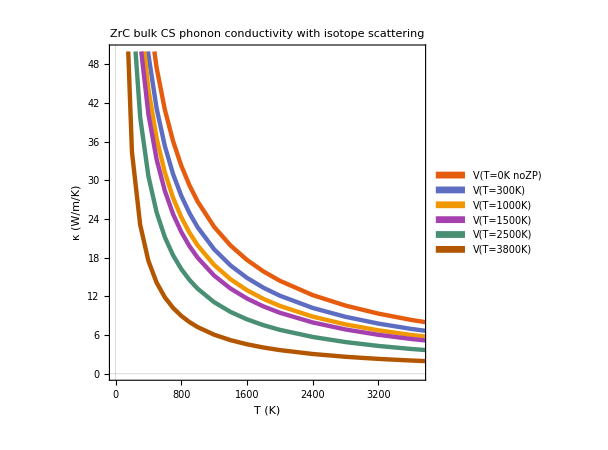
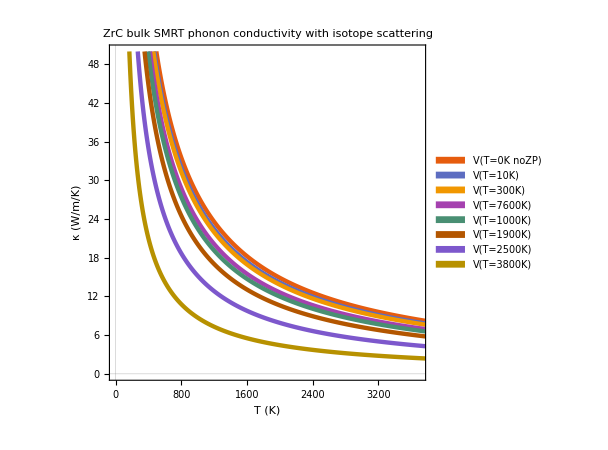

```mathematica
(*PloOptions*)
plotOptionsCS={AspectRatio->1,FrameLabel->{Style["T (K)",15],Style["κ (W/m/K)",15]},FrameTicksStyle->15,Frame->True,ImageSize->450,PlotLabel->Style["ZrC bulk CS phonon conductivity with isotope scattering",15],PlotRange->{{0,3700},{0,50}},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]],PlotLegends->SwatchLegend[{"V(T=0K noZP)", "V(T=300K)", "V(T=1000K)","V(T=1500K)","V(T=2500K)" ,"V(T=3800K)"}]};
plotOptionsPh={AspectRatio->1,FrameLabel->{Style["T (K)",15],Style["κ (W/m/K)",15]},FrameTicksStyle->15,Frame->True,ImageSize->450,PlotLabel->Style["ZrC bulk SMRT phonon conductivity with isotope scattering",15],PlotRange->{{0,3700},{0,50}},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]],PlotLegends->SwatchLegend[{"V(T=0K noZP)","V(T=10K)", "V(T=300K)", "V(T=7600K)","V(T=1000K)","V(T=1900K)","V(T=2500K)" ,"V(T=3800K)"}]};
(*Plot*)
With[{b1=6,b2=6},Show[{ListLinePlot[{kappa0[[b2]],kappa10[[b2]],kappa300[[b2]],kappa760[[b2]],kappa1000[[b2]],kappa1500[[b2]],kappa2500[[b2]],kappa3800[[b2]]},Evaluate@plotOptionsPh]}]]ListLinePlot[{condCS[[1]],condCS[[2]],condCS[[3]],condCS[[4]],condCS[[5]],condCS[[6]]},Evaluate@plotOptionsCS]
```

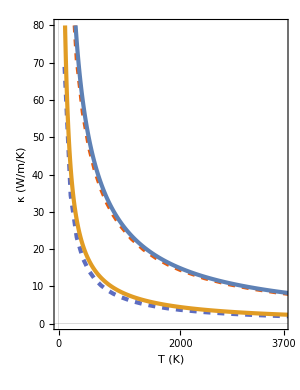

```mathematica
plotOptionsCS2={AspectRatio->1.3,FrameLabel->{Style["T (K)",20],Style["κ (W/m/K)",20]},FrameTicksStyle->20,Frame->True,ImageSize->300,PlotLabel->Style["",20],FrameTicks->{{Automatic,None},{{0,1000,2000,3000,3700},None}},FrameStyle->Directive[Thickness[0.01],20,Black],PlotRange->{{0,3700},{0,80}},PlotTheme->"Scientific",PlotStyle->Directive[Dashed,Thickness[0.01]],PlotLegends->Placed[SwatchLegend[{Style["C.S. @ V_0",18],Style["C.S. @ V_MP",18]}],{Right,Top}]};
plotOptionsPh2={AspectRatio->1.3,FrameLabel->{Style["T (K)",20],Style["κ (W/m/K)",20]},FrameTicksStyle->20,Frame->True,ImageSize->300,PlotLabel->Style["",20],FrameStyle->Directive[Thickness[0.01],20,Black],PlotRange->{{0,3700},{0,80}},PlotStyle->Directive[Thickness[0.01]],PlotLegends->Placed[SwatchLegend[{Style["3^rd o.L.D. @ V_0",18,FontFamily->"Times"],Style["3^rd o.L.D. @ V_MP",18,FontFamily->"Times"]}],{Right,Top}]};
Show[{ListLinePlot[{condCS[[1]],condCS[[6]]},Evaluate@plotOptionsCS2],ListLinePlot[{kappa0[[6]],kappa3800[[6]]},Evaluate@plotOptionsPh2]}]
```

## Do n-point linear interpolation to get kappa(V;T)

```mathematica
tList={10,300,760,1000,1500,2500,3800};
tList2={1,3800};
tList3=tList/10;
tListCS={10,300,1000,1500,2500,3800};
(*nameList={"kappa0","kappa10","kappa300","kappa760","kappa1000","kappa1500","kappa2500","kappa3800"};*)
nameList={kappa10,kappa300,kappa760,kappa1000,kappa1500,kappa2500,kappa3800};
nameListnoZP={kappa0,kappa300,kappa760,kappa1000,kappa1500,kappa2500,kappa3800};
```

```mathematica
kappa[T_,size_]:=(1-(10*T-tList[[2]])/tList[[8]])*Transpose[kappa10[[size]]][[2]][[T]]+((10*T-tList[[2]])/tList[[8]])*Transpose[kappa3800[[size]]][[2]][[T]]
kappa2[T_,size_,T1_,T2_]:=(1-(10*T-tList[[T1]])/tList[[T2]])*Transpose[kappa10[[size]]][[2]][[T]]+((10*T-tList[[T1]])/tList[[T2]])*Transpose[kappa3800[[size]]][[2]][[T]]
kappa3[T_,size_,T1_,T2_]:=(1-(10*T-tList[[T1]])/tList[[T2]])*Transpose[Evaluate[nameList[[T1]]][[size]]][[2]][[T]]+((10*T-tList[[T1]])/tList[[T2]])*Transpose[Evaluate[nameList[[T2]]][[size]]][[2]][[T]]
(*T=temperature*)
(*size = {1..6 for 0.01bmf iso to BULK iso. 7 is bulk perf*)
(*T1= 10 300 760 1000 1500 2500*)
(*T2= 300 760 1000 1500 2500 3800*)
kappa4[T_,size_,T1_,T2_]:=(1-((10*T-tList[[T1]])/(tList[[T2]]-tList[[T1]])))*Transpose[Evaluate[nameList[[T1]]][[size]]][[2]][[T]]+(((10*T-tList[[T1]])/(tList[[T2]]-tList[[T1]])))*Transpose[Evaluate[nameList[[T2]]][[size]]][[2]][[T]]
kappa4noZP[T_,size_,T1_,T2_]:=(1-((10*T-tList[[T1]])/(tList[[T2]]-tList[[T1]])))*Transpose[Evaluate[nameListnoZP[[T1]]][[size]]][[2]][[T]]+(((10*T-tList[[T1]])/(tList[[T2]]-tList[[T1]])))*Transpose[Evaluate[nameListnoZP[[T2]]][[size]]][[2]][[T]]
```

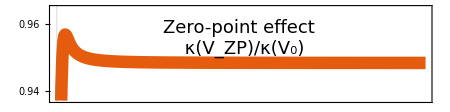

```mathematica
Show zero point effects;
 Look at the ZP effect on kappa at fixed volume;
plotOptionsZP={AspectRatio->0.25,FrameLabel->{Style["",20,Black],""},PlotLabels->Placed[Style["Zero-point effect \n κ(V_ZP)/κ(V_0)",18,Black],{0.5,0.99}],FrameTicksStyle->Directive[20,Black],Frame->True,FrameTicks->{{{0.94,0.95,0.96},None},{None,None}},ImageSize->450,PlotLabel->Style["",20],PlotRange->{{0,4000},{0.937,0.965}},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.02]]};
pZP=ListLinePlot[Transpose[{Transpose[kappa0[[7]]][[1]],Transpose[kappa10[[7]]][[2]]/Transpose[kappa0[[7]]][[2]]}],Evaluate@plotOptionsZP]
```

```mathematica
kappa10to1000bulk=Table[Join[Table[{T*10,kappa3[T,boundarySize,2,3]},{T,1,30}],Table[{T*10,kappa3[T,boundarySize,3,4]},{T,30,76}],Table[{T*10,kappa3[T,boundarySize,4,5]},{T,76,100}]],{boundarySize,1,1}];
```

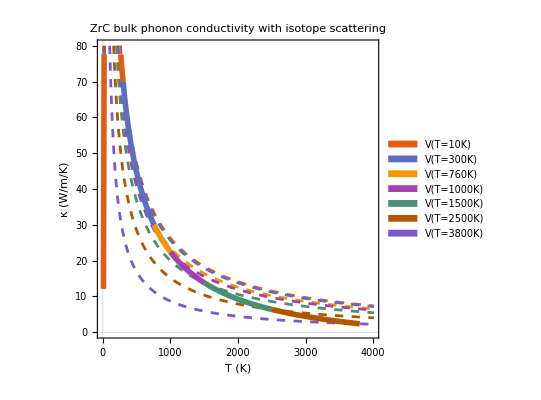

```mathematica
kappaOpts1={FrameLabel->{Style["T (K)",20],Style["κ (W/m/K)",20]},FrameTicksStyle->20,Frame->True,AspectRatio->1,PlotStyle->Directive[Dashing[0.015],Thickness[0.005]],PlotRange->{{0,4000},{0,80}},PlotLegends->Placed[SwatchLegend[{Style["V(T=10K)",18],Style["V(T=300K)",18],Style["V(T=760K)",18],Style["V(T=1000K)",18],Style["V(T=1500K)",18],Style["V(T=2500K)",18],Style["V(T=3800K)",18]}],{0.8,0.75}],PlotLabel->Style["ZrC bulk phonon conductivity with isotope scattering",15],PlotTheme->"Scientific",ImageSize->400};
kappaOpts2={AspectRatio->1,PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.01]]};

With[{size=4},Show[{ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},Evaluate@kappaOpts1],ListLinePlot[{Table[{T*10,kappa4[T,size,1,2]},{T,1,30}],Table[{T*10,kappa4[T,size,2,3]},{T,30,76}],Table[{T*10,kappa4[T,size,3,4]},{T,76,100}],Table[{T*10,kappa4[T,size,4,5]},{T,100,150}],Table[{T*10,kappa4[T,size,5,6]},{T,150,250}],Table[{T*10,kappa4[T,size,6,7]},{T,250,380}]},Evaluate@kappaOpts2]}]]
```

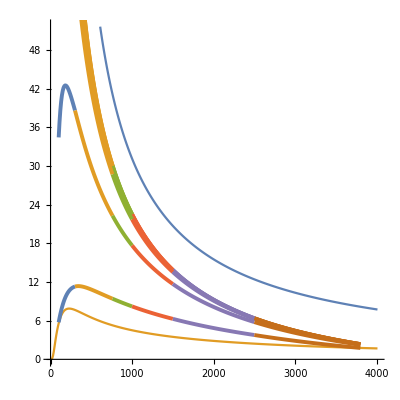

```mathematica
Show[{ListLinePlot[{kappa10[[7]],kappa3800[[1]]},AspectRatio->1],Table[With[{size=8-i},ListLinePlot[{Table[{T*10,kappa4[T,size,1,2]},{T,10,30}],Table[{T*10,kappa4[T,size,2,3]},{T,30,76}],Table[{T*10,kappa4[T,size,3,4]},{T,76,100}],Table[{T*10,kappa4[T,size,4,5]},{T,100,150}],Table[{T*10,kappa4[T,size,5,6]},{T,150,250}],Table[{T*10,kappa4[T,size,6,7]},{T,250,380}]},PlotStyle->Directive[Thickness[0.007]],PlotRange->{{50,3000},{0,200}}]],{i,2,7}]}]
```

## Illustrate variable volume SMRT kappa(V,T)

```mathematica
plotOptions={AspectRatio->1,FrameLabel->{Style["T (K)",15],Style["κ (W/m/K)",15]},FrameTicksStyle->15,Frame->True,ImageSize->450,PlotLabel->Style["ZrC bulk phonon conductivity with isotope scattering",15],PlotRange->{{0,3700},{0,50}},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]],PlotLegends->SwatchLegend[{"V(T=10K)","V(T=300K)","V(T=760K)","V(T=1000K)","V(T=1500K)","V(T=2500K)","V(T=3800K)"}]};
plotOptions1={AspectRatio->1,FrameLabel->{Style["T (K)",15],Style["κ (W/m/K)",15]},FrameTicksStyle->15,Frame->True,ImageSize->450,PlotLabel->Style["ZrC bulk phonon conductivity with isotope scattering",15],PlotRange->{{0,3700},{0,50}},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]]};
```

```mathematica
SMRTkappaVTbulk=With[{size=6},Table[Table[{T*10,kappa4[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}]];
SMRTkappaVTbulknoZP=With[{size=6},Table[Table[{T*10,kappa4noZP[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}]];
```

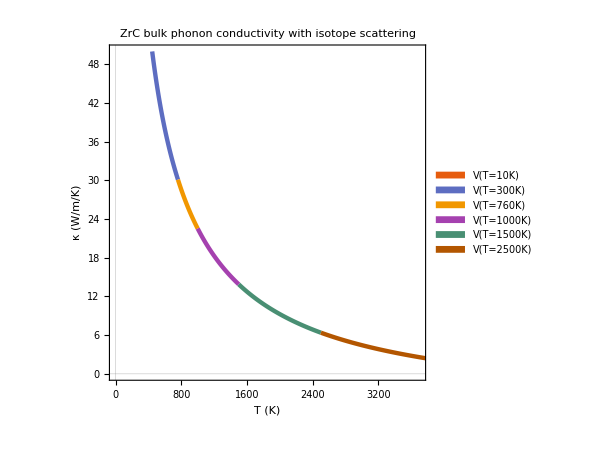

```mathematica
ListLinePlot[With[{size=6},Table[Table[{T*10,kappa4[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}]],Evaluate@plotOptions]
```

```mathematica
Illustrate variable volume CS kappa(V,T);
```

```mathematica
(*"V(T=0K)", "V(T=300K)", "V(T=1000K)","V(T=1500K)","V(T=2500K)" ,"V(T=3800K)";*)
csTemps={100,200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2400,2800,3200,3600,4000};
```

#### Interpolated CS kappa(T) at different volumes

```mathematica
condCSinter=Table[Interpolation[condCS[[vol]]],{vol,1,Length[condCS]}];
```

InterpolatingFunction::dmval: Input value {1.08169} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

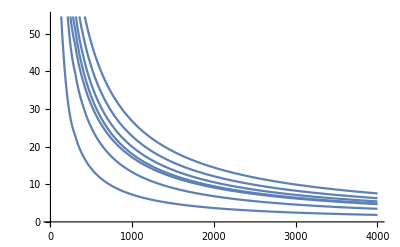

InterpolatingFunction::dmval: Input value {1.08169} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

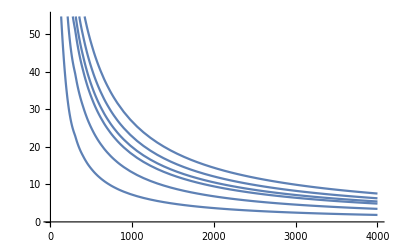

```mathematica
Plot[Table[condCSinter[[i]][t],{i,1,7}],{t,1,4000}]
Plot[Table[condCSinter[[i]][t],{i,1,6}],{t,1,4000}]
```

#### Re-express CS kappa in a basis with the same spacing as SMRT kappa ie 10K

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {30} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

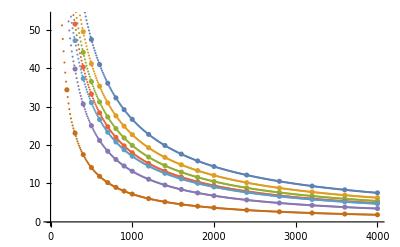

```mathematica
csKappadelta10K=Table[Table[{t,condCSinter[[vol]][t]},{t,10,4000,10}],{vol,1,Length[condCSinter]}];
Show[ListPlot[csKappadelta10K],ListPlot[condCS]]
```

```mathematica
kappa4CS[T_,T1_,T2_]:=(1-((10*T-tListCS[[T1]])/(tListCS[[T2]]-tListCS[[T1]])))*Transpose[csKappadelta10K[[T1]]][[2]][[T]]+(((10*T-tListCS[[T1]])/(tListCS[[T2]]-tListCS[[T1]])))*Transpose[csKappadelta10K[[T2]]][[2]][[T]]
```

#### Plot 6-point interpolated function

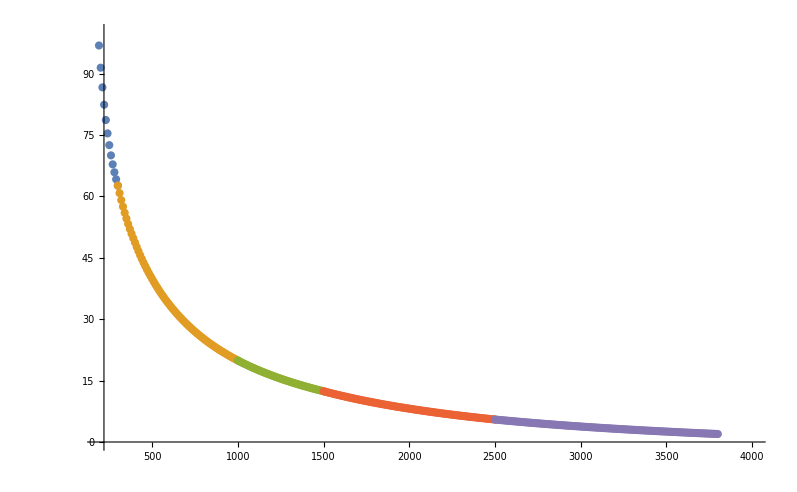

```mathematica
CSkappaVT=Table[Table[{10T,kappa4CS[T,vol,vol+1]},{T,tListCS[[vol]]/10,tListCS[[vol+1]]/10}],{vol,1,Length[tListCS]-1}];
ListPlot[CSkappaVT,PlotRange->{{200,4000},{0,100}}]
```

#### Compare to 2-part interpolation function, with and without SCPH

```mathematica
kappaCSvt2part=Table[{10T,(1-((10*T-tListCS[[1]])/(tListCS[[6]]-tListCS[[1]])))*Transpose[csKappadelta10K[[1]]][[2]][[T]]+(((10*T-tListCS[[1]])/(tListCS[[6]]-tListCS[[1]])))*Transpose[csKappadelta10K[[6]]][[2]][[T]]},{T,1,400}];
kappaCSvt2partSCPH=Table[{10T,(1-((10*T-tListCS[[1]])/(tListCS[[6]]-tListCS[[1]])))*Transpose[csKappadelta10K[[1]]][[2]][[T]]+(((10*T-tListCS[[1]])/(tListCS[[6]]-tListCS[[1]])))*Transpose[csKappadelta10K[[7]]][[2]][[T]]},{T,1,400}];
```

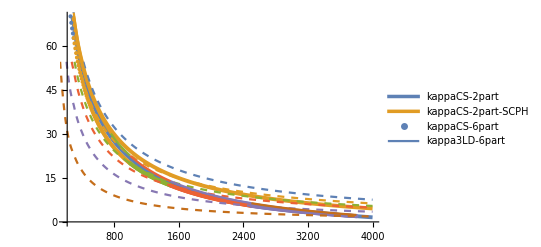

```mathematica
Show[{ListLinePlot[{kappaCSvt2part,kappaCSvt2partSCPH},PlotRange->{{200,4000},{0,70}},PlotStyle->Thickness[0.007],PlotLegends->{"kappaCS-2part","kappaCS-2part-SCPH"}],ListPlot[CSkappaVT,PlotLegends->{"kappaCS-6part"}],ListLinePlot[csKappadelta10K[[1;;6]],PlotStyle->Dashed],ListLinePlot[SMRTkappaVTbulknoZP,PlotLegends->{"kappa3LD-6part"}]}]
```

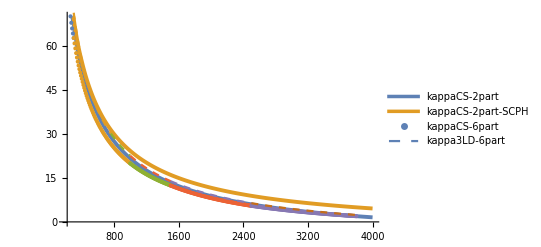

```mathematica
Show@{ListLinePlot[{kappaCSvt2part,kappaCSvt2partSCPH},PlotRange->{{200,4000},{0,70}},PlotStyle->Thickness[0.007],PlotLegends->{"kappaCS-2part","kappaCS-2part-SCPH"}],ListPlot[CSkappaVT,PlotLegends->{"kappaCS-6part"}],ListLinePlot[SMRTkappaVTbulknoZP,PlotStyle->Dashed,PlotLegends->{"kappa3LD-6part"}]}
```

#### Extract the kappa large displacement anharmonicity;

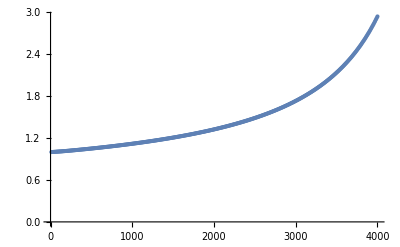

```mathematica
anhFactor=Transpose[kappaCSvt2partSCPH][[2]]/Transpose[kappaCSvt2part][[2]];
ListPlot@Transpose[{Transpose[kappaCSvt2partSCPH][[1]],anhFactor}]
```

#### Compare compressive sensing and 3LD;

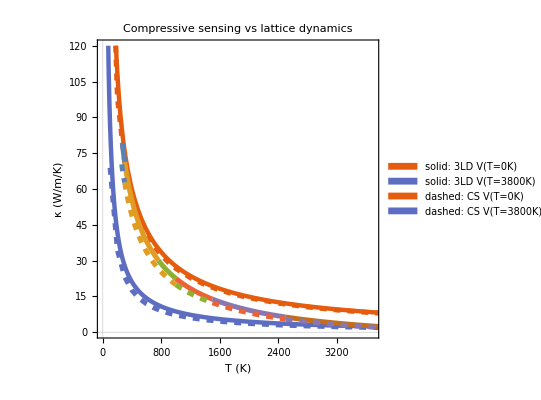

```mathematica
plotOptionsCS3={AspectRatio->1,FrameLabel->{Style["T (K)",20],Style["κ (W/m/K)",20]},FrameTicksStyle->20,Frame->True,ImageSize->400,PlotLabel->Style["Compressive sensing vs lattice dynamics",20],PlotRange->{{0,3700},{0,120}},PlotTheme->"Scientific",PlotStyle->Directive[{Thickness[0.009],Dashed}],PlotLegends->Placed[SwatchLegend[{Style["dashed:  CS V(T=0K)   ",18],Style["dashed:  CS V(T=3800K)  ",18]}],{0.618,0.75}]};
plotOptionsPh3={AspectRatio->1,FrameLabel->{Style["T (K)",20],Style["κ (W/m/K)",20]},FrameTicksStyle->20,Frame->True,ImageSize->400,PlotLabel->Style["Compressive sensing vs lattice dynamics",20],PlotRange->{{0,3700},{0,120}},PlotTheme->"Scientific",PlotStyle->Directive[{Thickness[0.008]}],PlotLegends->Placed[SwatchLegend[{Style["solid:  3LD V(T=0K)",18],Style["solid:  3LD V(T=3800K)",18]}],{0.6,0.9}]};
Show[{ListLinePlot[{kappa0[[6]],kappa3800[[6]]},Evaluate@plotOptionsPh3],ListLinePlot[{condCS[[1]],condCS[[6]]},Evaluate@plotOptionsCS3],ListLinePlot[SMRTkappaVTbulknoZP,PlotStyle->Directive[Thickness[0.009]]],ListLinePlot[CSkappaVT,PlotStyle->Directive[{Thickness[0.009],Dashed}]]}]
```

## Plot bulk kappa(V,T) with and without isotope scattering

```mathematica
plotOptionsIso={AspectRatio->1,FrameLabel->{Style["T (K)",20],Style["κ (W/m/K)",20]},FrameTicksStyle->20,Frame->True,ImageSize->400,PlotLabel->Style["Phonon-isotope scattering effect",20],PlotRange->{{0,3800},{0,60}},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.01]],PlotLegends->SwatchLegend[{Style["κ_(qha, iso)",20],Style["κ_iso",20]}]};
```

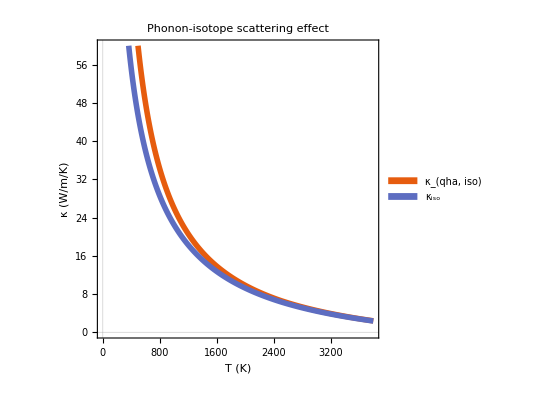

```mathematica
ListLinePlot[{With[{size=7},DeleteDuplicatesBy[Join@@Table[Table[{T*10,kappa4[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}],Last]],With[{size=6},DeleteDuplicatesBy[Join@@Table[Table[{T*10,kappa4[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}],Last]]},Evaluate@plotOptionsIso]
```

```mathematica
kappaNoIsobULK=With[{size=7},DeleteDuplicatesBy[Join@@Table[Table[{T*10,kappa4[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}],Last]];
kappaIsoBulk=With[{size=6},DeleteDuplicatesBy[Join@@Table[Table[{T*10,kappa4[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}],Last]];
kappaNoIsoOverIsoBulk=With[{size=6},DeleteDuplicatesBy[Join@@Table[Table[{T*10,kappa4[T,size+1,i,i+1]/kappa4[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}],Last]];
```

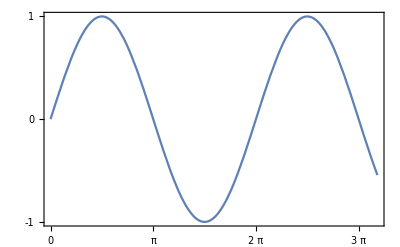

```mathematica
Plot[Sin[x],{x,0,10},Frame->True,FrameTicks->{{{-1,0,1},None},{{0,Pi,2 Pi,3 Pi},None}}]
```

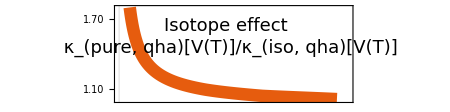

```mathematica
plotOptionsIso2={AspectRatio->0.25,FrameLabel->{Style["",20],""},FrameTicks->{{{{1.1,"1.10"},{1.4,"1.40"},{1.7,"1.70"}},None},{None,None}},FrameTicksStyle->Directive[20,Black],Frame->True,ImageSize->450,PlotLabel->Style["",20],PlotRange->{{0,4000},{1.00,1.8}},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.02]],PlotLabels->Placed[Style["Isotope effect \n κ_(pure, qha)[V(T)]/κ_(iso, qha)[V(T)]",18],{0.5,0.1}]};
pIso=ListLinePlot[kappaNoIsoOverIsoBulk,Evaluate@plotOptionsIso2]
```

## LogListPlot

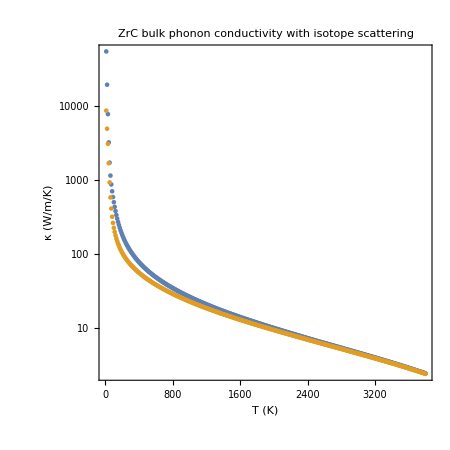

```mathematica
plotOptions1={Frame->True,FrameTicks->Automatic,AspectRatio->1,FrameLabel->{Style["T (K)",15],Style["κ (W/m/K)",15]},ImageSize->450,PlotLabel->Style["ZrC bulk phonon conductivity with isotope scattering",15],PlotRange->{{0,3700},{0,10}},PlotStyle->Directive[Thickness[0.007]]};

ListLogPlot[{With[{size=7},DeleteDuplicatesBy[Join@@Table[Table[{T*10,kappa4[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}],Last]],With[{size=6},DeleteDuplicatesBy[Join@@Table[Table[{T*10,kappa4[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}],Last]]},Evaluate@plotOptions1]
```

## Plot kappa(T) for different volumes, for 0.01micron and bulk

```mathematica
(*PlotLegends->Placed[SwatchLegend[{Style["1MBTE-LD - 0 K volume (NO ZP corrections)",15],Style["1MBTE-LD - MP volume",15]}],{0.53,0.87}]*)
plotOptions={AspectRatio->1,FrameLabel->{Style["T (K)",15],Style["κ (W/m/K)",15]},FrameTicksStyle->15,Frame->True,ImageSize->450,PlotLabel->Style["ZrC bulk phonon conductivity with isotope scattering",15],PlotRange->{{0,3700},{0,50}},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]],PlotLegends->SwatchLegend[{"V(T=10K)","V(T=300K)","V(T=760K)","V(T=1000K)","V(T=1500K)","V(T=2500K)","V(T=3800K)"}]};
p001=With[{size=1},ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},Evaluate[plotOptions]]];
p01=With[{size=2},ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},Evaluate[plotOptions]]];
p1=With[{size=3},ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},Evaluate[plotOptions]]];
p10=With[{size=4},ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},Evaluate[plotOptions]]];
p100=With[{size=5},ListLinePlot[{kappa10[[size]],kappa300[[size]],kappa760[[size]],kappa1000[[size]],kappa1500[[size]],kappa2500[[size]],kappa3800[[size]]},Evaluate[plotOptions]]];
```

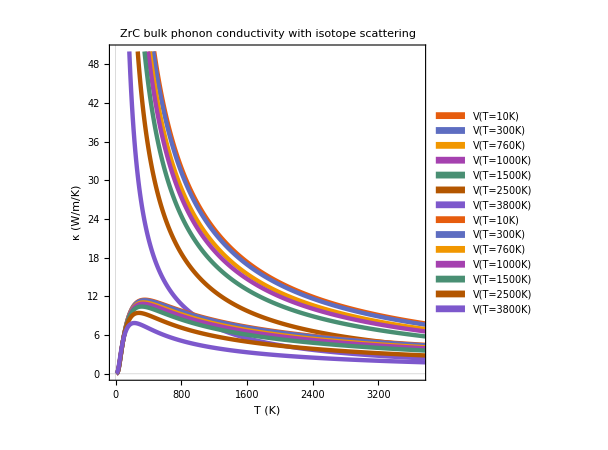

```mathematica
Show[p100,p001]
```

## Show kappa(V,T) at different boundary sizes

```mathematica
kappaVTbulk=With[{size=6},DeleteDuplicatesBy[Join@@Table[Table[{T*10,kappa4[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}],Last]];
kappaVT100bmf=With[{size=5},DeleteDuplicatesBy[Join@@Table[Table[{T*10,kappa4[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}],Last]];
kappaVT10bmf=With[{size=4},DeleteDuplicatesBy[Join@@Table[Table[{T*10,kappa4[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}],Last]];
kappaVT1bmf=With[{size=3},DeleteDuplicatesBy[Join@@Table[Table[{T*10,kappa4[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}],Last]];
kappaVT01bmf=With[{size=2},DeleteDuplicatesBy[Join@@Table[Table[{T*10,kappa4[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}],Last]];
kappaVT001bmf=With[{size=1},DeleteDuplicatesBy[Join@@Table[Table[{T*10,kappa4[T,size,i,i+1]},{T,Evaluate@tList3[[i]],Evaluate@tList3[[i+1]]}],{i,1,6}],Last]];
kappaV0Tbulk=kappa10[[6]];
kappaV0T100bmf=kappa10[[5]];
kappaV0T10bmf=kappa10[[4]];
kappaV0T1bmf=kappa10[[3]];
kappaV0T01bmf=kappa10[[2]];
kappaV0T001bmf=kappa10[[1]];
```

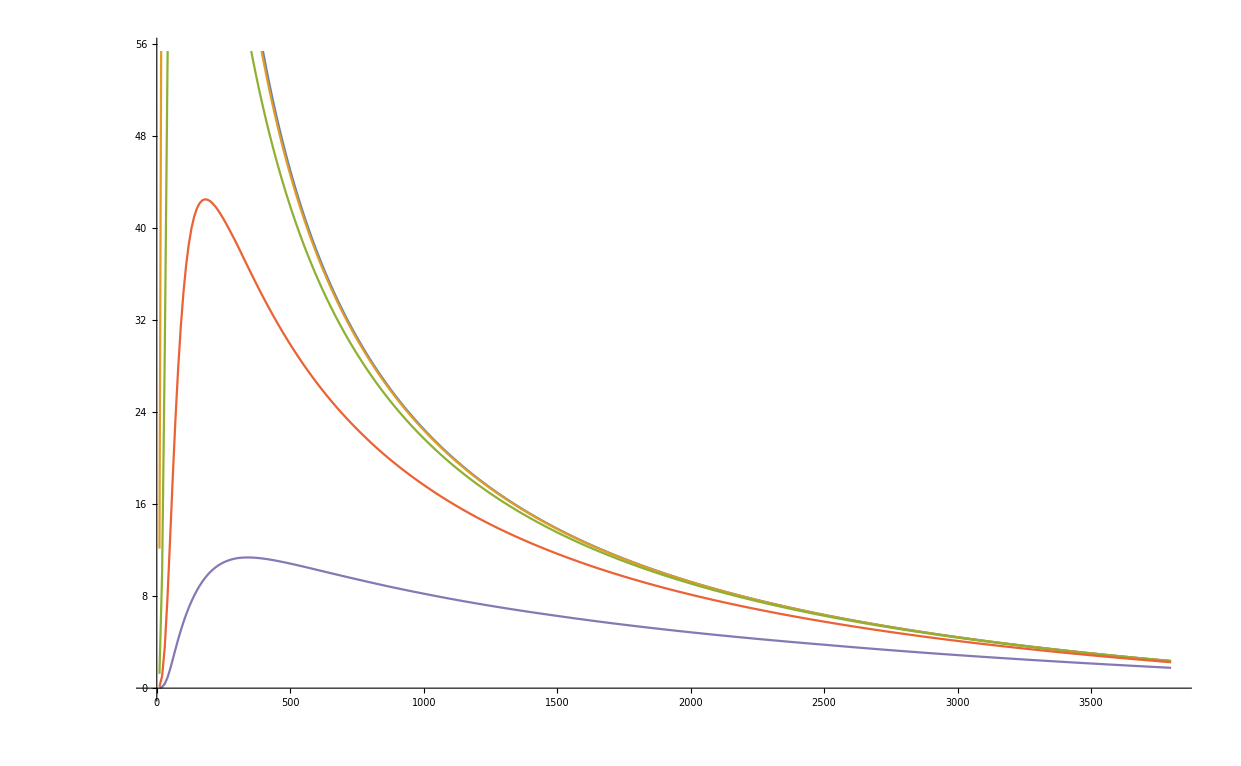

```mathematica
ListLinePlot[{kappaVT100bmf,kappaVT10bmf,kappaVT1bmf,kappaVT01bmf,kappaVT001bmf}]
```

```mathematica
Find f(V,T)=kappa(V;T)/Kappa(V0;T)
```

InterpolatingFunction::dmval: Input value {0.0817143} lies outside the range of data in the interpolating function. Extrapolation will be used.

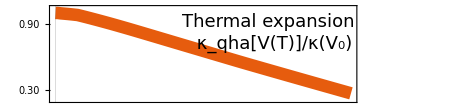

```mathematica
(*Old way - this ridiculus averaging was necessary before in order to deal with the duplicates
Join[Table[{-500+i,1},{i,1,500}],Table[{10i,Transpose[kappaVT100bmf][[2]][[i]]/Transpose[kappaV0T100bmf][[2]][[i]]},{i,1,Transpose[kappaVT100bmf][[2]]//Length}]];
MovingMap[GeometricMean,%,{500,Center},Automatic];*)
Table[{10i,Transpose[kappaVT100bmf][[2]][[i]]/Transpose[kappaV0T100bmf][[2]][[i]]},{i,1,Transpose[kappaVT100bmf][[2]]//Length}];
fVT=Interpolation[%];
plotOptionsVol={AspectRatio->0.25,FrameLabel->{Style["",20],Style["",20]},FrameTicksStyle->Directive[20,Black],Frame->True,ImageSize->450,FrameTicks->{{{{0.3,"0.30"},{0.6,"0.60"},{0.9,"0.90"}},None},{None,None}},PlotLabel->Style["",20],PlotLabels->Placed[Style["Thermal expansion \n κ_qha[V(T)]/κ(V_0)",18],{0.73,0.75}],PlotRange->{{0,4000},{0.2,1.05}},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.02]]};
pQha=Plot[fVT[x],{x,0,4000},Evaluate@plotOptionsVol]
```

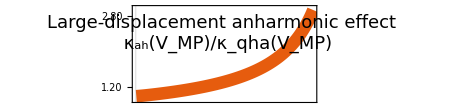

```mathematica
plotOptionsAnhVmp={AspectRatio->0.25,FrameLabel->{Style["",20,Black],Style["",20,Black]},FrameTicksStyle->Directive[20,Black],Frame->True,FrameTicks->{{{{1.2,"1.20"},{2,"2.00"},{2.8,"2.80"}},None},{None,None}},ImageSize->450,PlotRange->{{0,4000},{0.9,3}},PlotLabels->Placed[Style["Large-displacement anharmonic effect \n κ_ah(V_MP)/κ_qha(V_MP)",18],{0.5,0.73}],PlotLabel->Style["",20],PlotRange->{All},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.02]]};
pAnh=ListLinePlot[Transpose[{Transpose[kappaCSvt2partSCPH][[1]],anhFactor}],Evaluate@plotOptionsAnhVmp]
```

## Plot kappa vs boundary size

```mathematica
kappaBoundarytList=Table[{{-2,kappaVT001bmf[[tList[[i]]/10]][[2]]},{-1,kappaVT01bmf[[tList[[i]]/10]][[2]]},{0,kappaVT1bmf[[tList[[i]]/10]][[2]]},{1,kappaVT10bmf[[tList[[i]]/10]][[2]]},{2,kappaVT100bmf[[tList[[i]]/10]][[2]]},{3,kappaVTbulk[[tList[[i]]/10]][[2]]}},{i,1,7}]
```

{{{-2,0.0124921953791471072},{-1,0.12488086337771144},{0,1.24486778687541611},{1,12.133120959193489},{2,105.743314366258758},{3,8704.97856395416056}},{{-2,11.2964376520326724},{-1,38.6128434649567751},{0,62.6859425610499628},{1,69.9384102086162187},{2,71.1178659962515809},{3,71.264165255852447}},{{-2,9.41046502438652333},{-1,22.2947314791027331},{0,28.7001136072730887},{1,29.9447284940031686},{2,30.0966231098534074},{3,30.1140062538596389}},{{-2,8.21605928035426558},{-1,17.6717260400760594},{0,21.7219363960764404},{1,22.4391901661458206},{2,22.5228201805316992},{3,22.5323087549616297}},{{-2,6.28370504269488617},{-1,11.6899854448489116},{0,13.5451539894745636},{1,13.8363426999008752},{2,13.8686398573987084},{3,13.8722746197355953}},{{-2,3.77704791443584709},{-1,5.78329050778305831},{0,6.29711468199471458},{1,6.3672097044149929},{2,6.37463030364886407},{3,6.37546007438315865}},{{-2,1.76824770776778584},{-1,2.25324548126163293},{0,2.34741724469985647},{1,2.35866921547611819},{2,2.35982282275315569},{3,2.35995132758971327}}}

```mathematica
plotOptions={AspectRatio->0.8,FrameLabel->{Style["L (10^xμm)  ",20,Black],Style["κ (W/mK)",20,Black]},FrameTicksStyle->Directive[20,Black],Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],ImageSize->400,PlotRange->{{-2,3},{0,105}},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.007]],PlotLegends->Placed[SwatchLegend[{Style["10K",20],Style["300K",20],Style["760K",20],Style["1000K",20],Style["1500K",20],Style["2500K",20],Style["3800K",20]}],{Left,Top}],ImageSize->500};
```

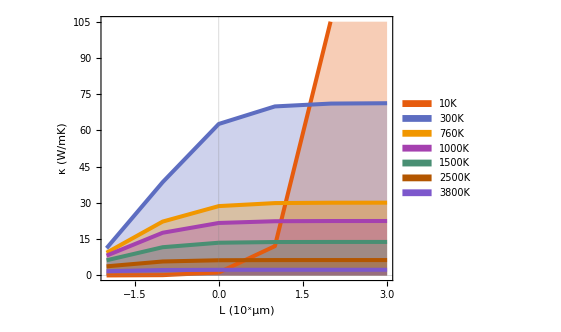

```mathematica
ListLinePlot[kappaBoundarytList,Filling->Bottom,Evaluate@plotOptions]
```

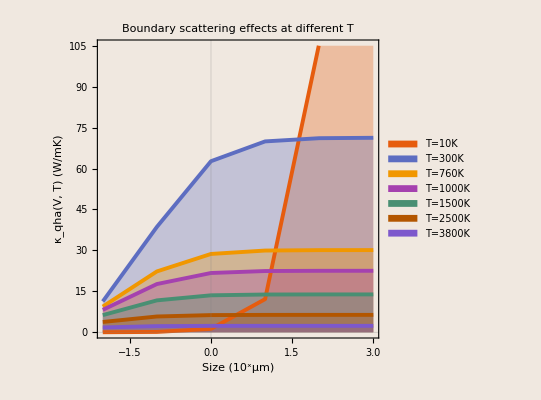

```mathematica
ListLinePlot[kappaBoundarytList,Filling->Bottom,Evaluate@plotOptions,Background->LightBrown]
```

## QHA Cp scaling

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/FRENKEL_RESULTS/Tall/PERF/1_fqh_fel/output_0.0001GPa/"];
qhaFiles={"heat_capacity_isochoric","volume_expansion","volume_expansion_coefficient","volume_expansion_relative","bulk_modulus_isothermal"};
qhaStuff=Table[ReadList[qhaFiles[[i]],{Number,Number}],{i,1,qhaFiles//Length}];
```

```mathematica
cP=Transpose[qhaStuff[[1]]][[2]];
V=Transpose[qhaStuff[[2]]][[2]];
alpha=Transpose[qhaStuff[[3]]][[2]];
VER=Transpose[qhaStuff[[4]]][[2]];
bulkMod=Transpose[qhaStuff[[4]]][[2]];
t=Transpose[qhaStuff[[1]]][[1]];
```

bulk is GPA
T in in Kelvin
alpha is in dimensionless (log vol derivtive) per kelvin
V is in angstrom^3/atom = alatt^3/8
Cp is in kBT/atom = 8.6173303(50)×10−5 eV/K

1 eV/Angstrom3 = 160.21766208 GPa
1GPa = (1/160.21766208)1 eV/Angstrom3

K*Ang^3*1/K^2*GPa

```mathematica
cpFactorRaw=With[{end=4000},(((8.6173303*10^-5)/(160.21766208))*t[[2;;end]]*alpha[[2;;end]]*alpha[[2;;end]]*bulkMod[[2;;end]])/(cP[[2;;end]])];
cPfactor=Transpose[{t[[2;;4000]],Evaluate[1/(1-cpFactorRaw)]}];
```

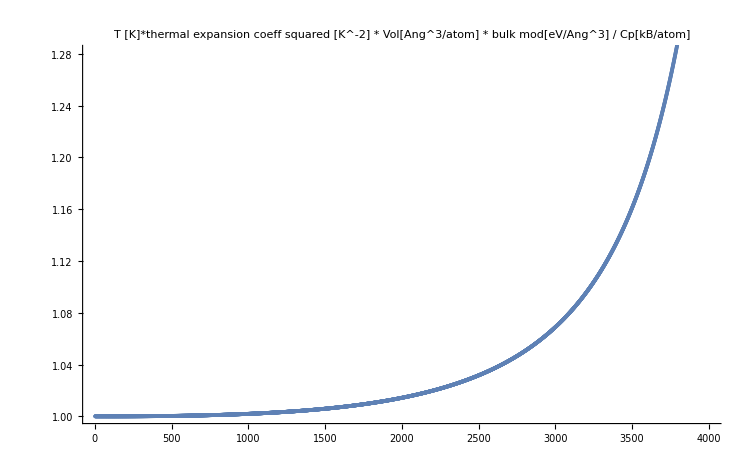

```mathematica
ListPlot[cPfactor,PlotLabel->"T [K]*thermal expansion coeff squared [K^-2] * Vol[Ang^3/atom] * bulk mod[eV/Ang^3] / Cp[kB/atom]"]
```

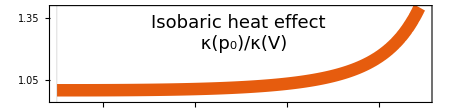

```mathematica
plotOptionscPfactor={AspectRatio->0.25,FrameLabel->{Style["",20],Style["",20]},FrameTicksStyle->Directive[20,Black],Frame->True,ImageSize->450,FrameTicks->{{{1.05,{1.2,"1.20"},1.35},None},{{500,1000,1500,2000,2500,3000,3500},None}},PlotRange->{{0,4000},{0.95,1.4}},PlotLabels->Placed[Style["Isobaric heat effect \n κ(p_0)/κ(V)",18],{0.5,0.6}],PlotLabel->Style["",20],PlotRange->{All},PlotTheme->"Scientific",PlotStyle->Directive[Thickness[0.02]]};
pCp=ListLinePlot[cPfactor,Evaluate@plotOptionscPfactor]
```

```mathematica
FrameTicks->{{{1.1,1.4,1.7},None},{None,None}}
```

FrameTicks→{{{1.1,1.4,1.7},None},{None,None}}

```mathematica
Show[pIso]
Show[pZP]
```

-Graphics-

-Graphics-

```mathematica
Column[{{pIso},{pZP},{pQha},{pAnh},{pCp}},ImageSize->900]
```

{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}
{-Graphics-}

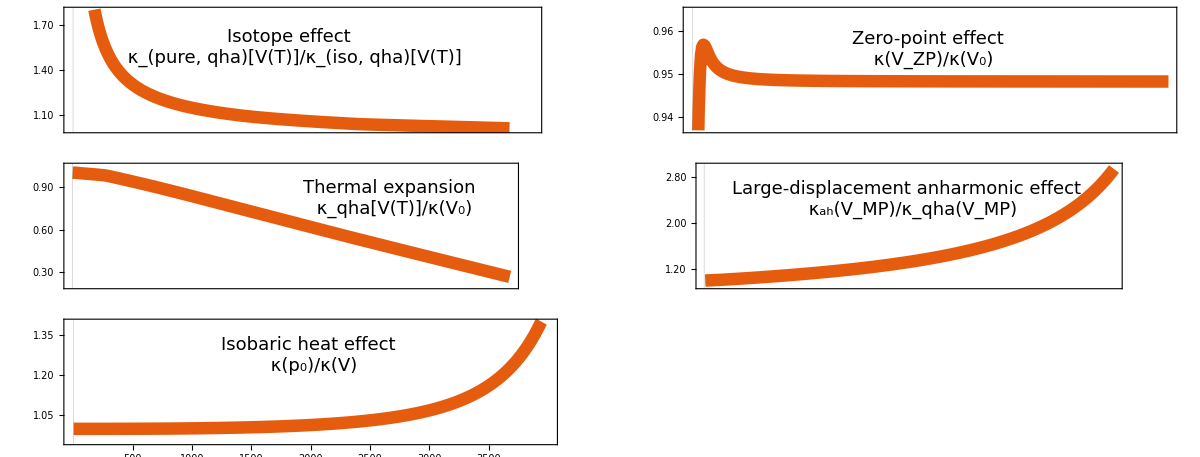

```mathematica
GraphicsGrid[{{pIso,pZP},{pQha,pAnh},{pCp}},ImageSize->1200]
```

```mathematica
(*Take from element 9 to -1 and sample every tenth, and take only the scaling column not the T column*)
```

```mathematica
kappaIsoBulkwithAnh=Transpose[{Transpose[kappaIsoBulk][[1]],anhFactor[[1;;380]]*Transpose[kappaIsoBulk][[2]]}];
(*For the Cp factor, Take from element 9 to -1 and sample every tenth, and take only the scaling column not the T column*)
kappaIsoBulkwithCp=Transpose[{Transpose[kappaIsoBulk][[1]],Transpose[cPfactor[[9;;-1;;10]]][[2]][[1;;380]]*Transpose[kappaIsoBulk][[2]]}];
kappaIsoBulkwithCpandAnh=Transpose[{Transpose[kappaIsoBulk][[1]],anhFactor[[1;;380]]*Transpose[cPfactor[[9;;-1;;10]]][[2]][[1;;380]]*Transpose[kappaIsoBulk][[2]]}];
```

#### Plot the final bulk rescale Cp, qha, anh, and iso kappa

```mathematica
pltBulkRescaled={AspectRatio->1,FrameLabel->{Style["T (K)",20],Style["κ (W/m/K)",20]},FrameTicksStyle->20,Frame->True,ImageSize->400,PlotLabel->Style["ZrC thermal conductivity",20],PlotRange->{{0,3700},{0,120}},PlotTheme->"Scientific",PlotStyle->Directive[{Thickness[0.009],Dashed}],PlotLegends->Placed[SwatchLegend[{Style["κ_(bulk, iso, qha)[V(T);T]",18],Style["κ_(bulk, iso, anh)[V(T);T]",18],Style["κ_(bulk, iso, qha)[p_0;T]",18],Style["κ_(bulk, iso, anh)[p_0;T]}",18]}],{0.618,0.75}]};
```

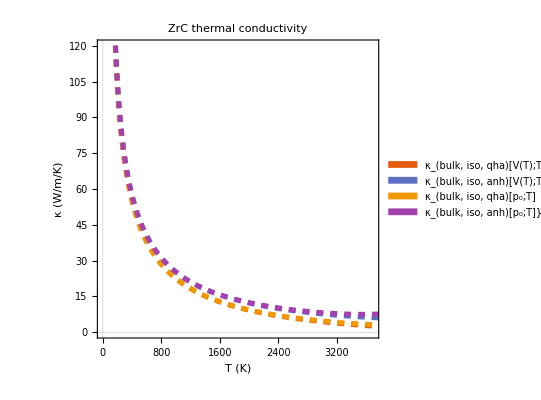

```mathematica
ListLinePlot[{kappaIsoBulk,kappaIsoBulkwithAnh,kappaIsoBulkwithCp,kappaIsoBulkwithCpandAnh},Evaluate@pltBulkRescaled]
```

```mathematica
Export["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/kappaIsoBulkwithCpandAnh.mx",kappaIsoBulkwithCpandAnh];
```

#### Plot the full kappa_ph at different particle sizes

{10,105.743314366258758}

380

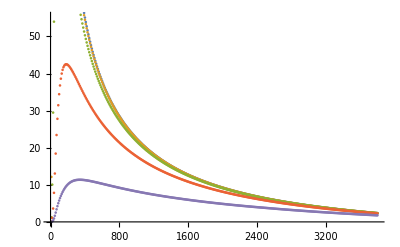

```mathematica
kappaVT100bmf[[1]]
kappaVT100bmf//Length
ListPlot[{kappaVT100bmf,kappaVT10bmf,kappaVT1bmf,kappaVT01bmf,kappaVT001bmf}]
```

```mathematica
Transpose[kappaVT100bmf][[1]]//Length
```

380

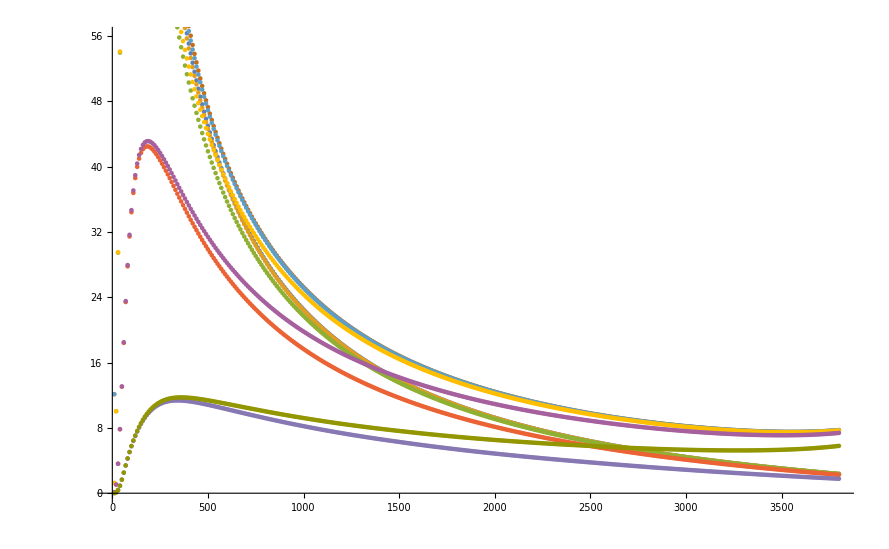

```mathematica
kappaIsoBulkwithCpandAnh100=Transpose[{Transpose[kappaIsoBulk][[1]],anhFactor[[1;;380]]*Transpose[cPfactor[[9;;-1;;10]]][[2]][[1;;380]]*Transpose[kappaVT100bmf][[2]]}];
kappaIsoBulkwithCpandAnh10=Transpose[{Transpose[kappaIsoBulk][[1]],anhFactor[[1;;380]]*Transpose[cPfactor[[9;;-1;;10]]][[2]][[1;;380]]*Transpose[kappaVT10bmf][[2]]}];
kappaIsoBulkwithCpandAnh1=Transpose[{Transpose[kappaIsoBulk][[1]],anhFactor[[1;;380]]*Transpose[cPfactor[[9;;-1;;10]]][[2]][[1;;380]]*Transpose[kappaVT1bmf][[2]]}];
kappaIsoBulkwithCpandAnh01=Transpose[{Transpose[kappaIsoBulk][[1]],anhFactor[[1;;380]]*Transpose[cPfactor[[9;;-1;;10]]][[2]][[1;;380]]*Transpose[kappaVT01bmf][[2]]}];
kappaIsoBulkwithCpandAnh001=Transpose[{Transpose[kappaIsoBulk][[1]],anhFactor[[1;;380]]*Transpose[cPfactor[[9;;-1;;10]]][[2]][[1;;380]]*Transpose[kappaVT001bmf][[2]]}];
ListPlot[{kappaVT100bmf,kappaVT10bmf,kappaVT1bmf,kappaVT01bmf,kappaVT001bmf,kappaIsoBulkwithCpandAnh100,kappaIsoBulkwithCpandAnh10,kappaIsoBulkwithCpandAnh1,kappaIsoBulkwithCpandAnh01,kappaIsoBulkwithCpandAnh001}]
```

```mathematica
Export["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/kappaIsoBulkwithCpandAnh100.mx",kappaIsoBulkwithCpandAnh100];
Export["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/kappaIsoBulkwithCpandAnh10.mx",kappaIsoBulkwithCpandAnh10];
Export["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/kappaIsoBulkwithCpandAnh1.mx",kappaIsoBulkwithCpandAnh1];
Export["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/kappaIsoBulkwithCpandAnh01.mx",kappaIsoBulkwithCpandAnh01];
Export["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/RESULTS_all_ZrC_kappa_ph_9March2017/kappaIsoBulkwithCpandAnh001.mx",kappaIsoBulkwithCpandAnh001];
```